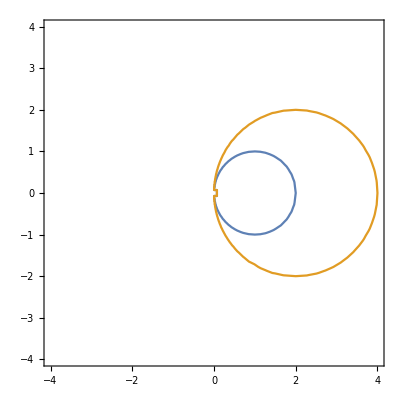

```mathematica
ContourPlot[{Re[1/(x+I y)]==1/2,Re[1/(x+I y)]==1/4},{x,-#1,#1},{y,-#1,#1}]&[4]
```

```mathematica
1/z^5 Series[Cos[z/(1-2 z)],{z,0,10}]
```

1/z^5-1/(2 z^3)-2/z^2-143/(24 z)-47/3-(27601 z)/720-(1787 z^2)/20-(8095583 z^3)/40320-(1103647 z^4)/2520-(3377674081 z^5)/3628800+O[z]^6

```mathematica
expansion=Series[1/z^(κ+1)(z-1)^(1/2),{z,0,10},Assumptions->κ==3&&Im[z]≠0]
```

Piecewise[{{-ⅈ/z^4+ⅈ/(2 z^3)+ⅈ/(8 z^2)+ⅈ/(16 z)+(5 ⅈ)/128+(7 ⅈ z)/256+(21 ⅈ z^2)/1024+(33 ⅈ z^3)/2048+(429 ⅈ z^4)/32768+(715 ⅈ z^5)/65536+(2431 ⅈ z^6)/262144+O[z]^7, Im[z]<0}, {ⅈ/z^4-ⅈ/(2 z^3)-ⅈ/(8 z^2)-ⅈ/(16 z)-(5 ⅈ)/128-(7 ⅈ z)/256-(21 ⅈ z^2)/1024-(33 ⅈ z^3)/2048-(429 ⅈ z^4)/32768-(715 ⅈ z^5)/65536-(2431 ⅈ z^6)/262144+O[z]^7, True}}]

```mathematica
SeriesCoefficient[expansion,-1]
```

SeriesCoefficient[Piecewise[{{-ⅈ/z^4+ⅈ/(2 z^3)+ⅈ/(8 z^2)+ⅈ/(16 z)+(5 ⅈ)/128+(7 ⅈ z)/256+(21 ⅈ z^2)/1024+(33 ⅈ z^3)/2048+(429 ⅈ z^4)/32768+(715 ⅈ z^5)/65536+(2431 ⅈ z^6)/262144+O[z]^7, Im[z]<0}, {ⅈ/z^4-ⅈ/(2 z^3)-ⅈ/(8 z^2)-ⅈ/(16 z)-(5 ⅈ)/128-(7 ⅈ z)/256-(21 ⅈ z^2)/1024-(33 ⅈ z^3)/2048-(429 ⅈ z^4)/32768-(715 ⅈ z^5)/65536-(2431 ⅈ z^6)/262144+O[z]^7, True}}],-1]

```mathematica
Limit[ϵ^(κ-1/2)E^(I θ(κ-3/2))(1-ϵ E^(I θ))^(1/2),ϵ->0,Assumptions->(κ>3/2)]
```

0